# Σ1 (p=0, ω)

```mathematica
SetDirectory["/home/h/H.Guertner/theorie/BEC_Polaron/Mathematica/"];
<<params.mx
```

## Integrand for ω1 Integral

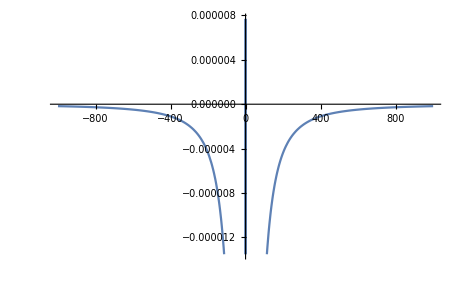

```mathematica
f[ q_, ω_, ω1_, ε_ ]:=4*ⅈ*Pi/(2*Pi)^4*q^2* vq2[q]*g0pw[q, ω-ω1,ε]*dqw[q,ω1,ε]*Exp[ⅈ*ω1*ε];
Plot[Limit[-ⅈ*f[1,1, w, eps],eps->0],{w, -1000,1000} ]
```

## Integrand for q Integral

```mathematica
w1pol:= ω1/.Solve[Denominator[f[ q, ω, ω1, ε1]]==0,ω1];
```

```mathematica
gres[q_,ω_, ε_ ]=Limit[2*Pi*ⅈ*Residue[f[ q, ω, ω1,ε1], {ω1, w1pol[[2]]}, Assumptions->ε1>0 ],ε1->0]
```

-((3.81972+0. ⅈ) q^2 √(q^2/(2+q^2)))/(4.+1. q^2+1. √(q^2 (2.+q^2))-2. ω)

```mathematica
8*Pi/(2*Pi)^3*q^2* vq2[q]
```

3.81972 q^2 √(q^2/(2+q^2))

```mathematica
g[q_,ω_, ε_ ]:=4*Pi/(2*Pi)^3*q^2* vq2[q]*-1/(ω-q^2/2+μ-wq[q]+ⅈ*ε);
```

```mathematica
Plot3D[g[q,w,0],{q, 0,qc} ,{w,-100,100}, MaxRecursion->5, PlotRange -> {-1,4}]
```

-Graphics3D-

## Σ1 with NIntegrate

```mathematica
ΣMC[ω_]:=NIntegrate[g[q, ω, 0],{q,0, qc}, Method -> "MonteCarlo"]
Σ[ω_]:=NIntegrate[g[q, ω, 0],{q,0, qc}]
```

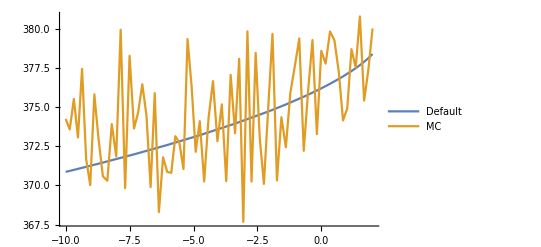

```mathematica
Plot[{Σ[w],ΣMC[w]},{w,-10,2},PlotPoints->10,MaxRecursion ->3,PlotRange->Full, PlotLegends-> {"Default", "MC"}]
```

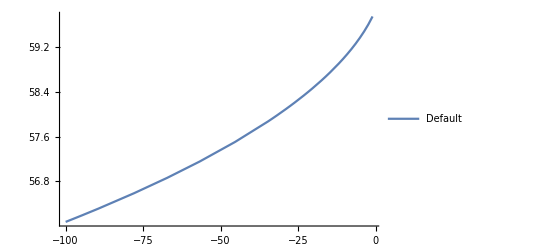

```mathematica
Plot[Σ[w],{w,-100,-1},PlotPoints->10,MaxRecursion ->3,PlotRange->Full, PlotLegends-> {"Default"}]
```

```mathematica
Σomegadata= Table[{τ, NIntegrate[g[q, ω, 0],{q,0, qc}]},{ω, -100, 2, 0.5}];
```

```mathematica
DumpSave["1st_SEw.mx",{Σ, Σomegadata}];
Export["mat_fo_sew", Σomegadata, "Table"];
```